```mathematica
f=Exp[-Log[x/(1.6)]^2]
```

ⅇ^(-Log[0.625 x]^2)

```mathematica
mv=MaxValue[f,x]
```

1.

```mathematica
am=ArgMax[f,x]
```

1.6

```mathematica
last=10
```

10

```mathematica
peakPoint={am,mv}
peakPointBotom={am,0}
peakZero={0,mv}
```

{1.6,1.}

{1.6,0}

{0,1.}

```mathematica
x["d"]=8
c["d"]=f/.x->x["d"]//N
x["d-1"]=7.5
c["d-1"]=f/.x->x["d-1"]//N
```

8

0.0749983

7.5

0.0919313

```mathematica
arrowY=0.066
arrow1=Arrow[{{0,arrowY},{am,arrowY}}]
arrow2=Arrow[{{am,arrowY},{x["d"],arrowY}}]
arrow3=Arrow[{{x["d"],arrowY},{last,arrowY}}]
```

0.066

Arrow[{{0,0.066},{1.6,0.066}}]

Arrow[{{1.6,0.066},{8,0.066}}]

Arrow[{{8,0.066},{10,0.066}}]

```mathematica
textPk=Text["Peak count",{-0.45,1}]
textPY=Text["Publish year",{-0.5,-0.09}]
textFC=Text["First cited\nyear",{0.5,-0.09}]
textPkY=Text["Peak year",{1.8,-0.09}]
textDY=Text["Decay year",{8.5,-0.09}]
textLY=Text["Last year",{10.5,-0.09}]
textPd1=Text["Peak period",{0.9,0.1}]
textPd2=Text["Decay period",{4,0.1}]
textPd3=Text["Sustain period",{9,0.1}]
textX0=Text[Style["0",17],{-0.05,-0.01}]
textXc=Text[Style["x_c",17],{0.4,-0.01}]
textXp=Text[Style["x_p",17],{1.6,-0.01}]
textXd1=Text[Style["x_(d - 1)",17],{7.4,-0.01}]
textXd=Text[Style["x_d",17],{8,-0.01}]
textXl=Text[Style["x_l",17],{10,-0.01}]
```

Text[Peak count,{-0.45,1}]

Text[Publish year,{-0.5,-0.09}]

Text[First cited
year,{0.5,-0.09}]

Text[Peak year,{1.8,-0.09}]

Text[Decay year,{8.5,-0.09}]

Text[Last year,{10.5,-0.09}]

Text[Peak period,{0.9,0.1}]

Text[Decay period,{4,0.1}]

Text[Sustain period,{9,0.1}]

Text[0,{-0.05,-0.01}]

Text[x_c,{0.4,-0.01}]

Text[x_p,{1.6,-0.01}]

Text[x_(d - 1),{7.4,-0.01}]

Text[x_d,{8,-0.01}]

Text[x_l,{10,-0.01}]

{Line[{{7.5,0},{7.5,0.0919313}}],Line[{{8,0},{8,0.0749983}}],Line[{{10,0},{10,0.1}}],Arrowheads[{-0.025,0.025}],Arrow[{{0,0.066},{1.6,0.066}}],Arrow[{{1.6,0.066},{8,0.066}}],Arrow[{{8,0.066},{10,0.066}}],Dashing[{Small,Small}],Line[{{1.6,1.},{1.6,0}}],Line[{{1.6,1.},{0,1.}}],Text[Peak count,{-0.45,1}],Text[Publish year,{-0.5,-0.09}],Text[First cited
year,{0.5,-0.09}],Text[Peak year,{1.8,-0.09}],Text[Decay year,{8.5,-0.09}],Text[Last year,{10.5,-0.09}],Text[Peak period,{0.9,0.1}],Text[Decay period,{4,0.1}],Text[Sustain period,{9,0.1}],Text[0,{-0.05,-0.01}],Text[x_c,{0.4,-0.01}],Text[x_p,{1.6,-0.01}],Text[x_(d - 1),{7.4,-0.01}],Text[x_d,{8,-0.01}],Text[x_l,{10,-0.01}]}

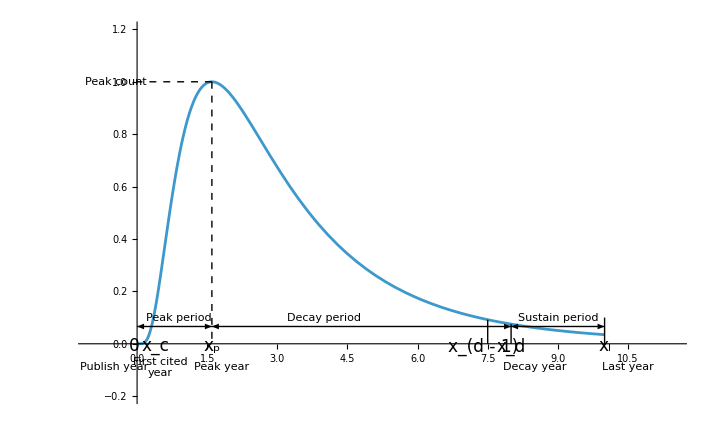

```mathematica
epob={Line[{{x["d-1"],0},{x["d-1"],c["d-1"]}}],Line[{{x["d"],0},{x["d"],c["d"]}}],Line[{{last,0},{last,0.1}}],Arrowheads[{-0.025,0.025}],arrow1,arrow2,arrow3,Dashed,Line[{peakPoint,peakPointBotom}],Line[{peakPoint,peakZero}],textPk,textPY,textFC,textPkY,textDY,textLY,textPd1,textPd2,textPd3,textX0,textXc,textXp,textXd1,textXd,textXl}
Plot[f,{x,0,last},Ticks->None,Epilog->epob,PlotRange->{{-1,last+1.5},{-0.2,1.2}}]
```